1.)

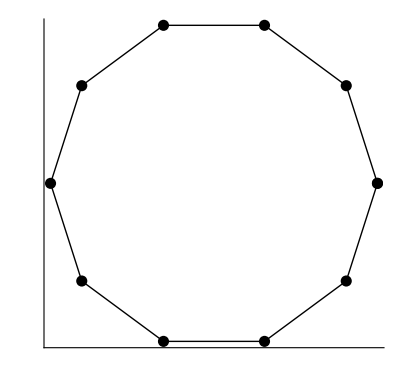

```mathematica
Graphics[
{
Thick,Line[{Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}]}],
PointSize[0.02],
Point[
Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}]
]
},
Axes->True,
Ticks->None
]
```

2.)

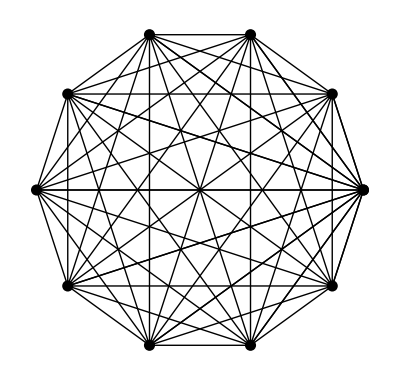

```mathematica
Graphics[
{
Thick,Line[Subsets[Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}],{2}]],
PointSize[0.02],
Point[
Table[{Cos[2Pi x/10],Sin[2Pi x/10]},{x,0,10,1}]
]
}
]
```

3.)

```mathematica
Manipulate[
Graphics[
{
Thick,Line[Subsets[Table[{Cos[2Pi x/n],Sin[2Pi x/n]},{x,0,n,1}],{2}]],
PointSize[0.02],
Point[
Table[{Cos[2Pi x/n],Sin[2Pi x/n]},{x,0,n,1}]
]
}
],
{{n,16},3,20,1}
]
```

4.)

```mathematica
Graphics[
{
PointSize[0.02],
Rotate[Point[Table[{Cos[2Pi x/6],Sin[2Pi x/6]},{x,0,10,1}]],Pi/2],
Point[{{Sqrt[3],0},{-Sqrt[3]/2,1.5},{-Sqrt[3]/2,-1.5}}],
Thick,Circle[{2/3(Sqrt[3]),0},1/3Sqrt[3],{4/3Pi,8/3Pi}],
Circle[{-1/3(Sqrt[3]),1},1/3Sqrt[3],{0,4/3Pi}],
Circle[{-1/3(Sqrt[3]),-1},1/3Sqrt[3],{2/3Pi,2Pi}],
Circle[{1/3(Sqrt[3]),1},1/3Sqrt[3],{Pi,5/3Pi}],
Circle[{1/3(Sqrt[3]),-1},1/3Sqrt[3],{1/3Pi,Pi}],
Circle[{-2/3(Sqrt[3]),0},1/3Sqrt[3],{5/3Pi,7/3Pi}]
},
ImageSize->Medium
]
```

-Graphics-